```mathematica
Clear[n];
Clear[a];
```

```mathematica
f[x_]=x^n-a;
φ[x_]=x-f[x]/(f'[x])
φ'[x]
n=5;
a=9;
N[NestList[φ,2,3]]
N[a^(1/n)]
Reduce[{φ'[x]<1, φ'[x]>-1,n∈Reals,a∈Reals},x∈Reals]
```

x-(x^(1-n) (-a+x^n))/n

-((1-n) x^-n (-a+x^n))/n

{2.,1.7125,1.57929,1.55278}

1.55185

x<-6^(2/5)||x>2^(2/5)

```mathematica
f[x_]=x^3-4x^2+5x-2
φ[x_]=x-f[x]/(f'[x])
φ'[x]
φ'[0]
φ[0]
Limit[φ[x],x->1]
```

-2+5 x-4 x^2+x^3

x-(-2+5 x-4 x^2+x^3)/(5-8 x+3 x^2)

((-8+6 x) (-2+5 x-4 x^2+x^3))/((5-8 x+3 x^2)^2)

16/25

2/5

1

```mathematica
Solve[f[x]==0,x]
```

{{x→1},{x→1},{x→2}}

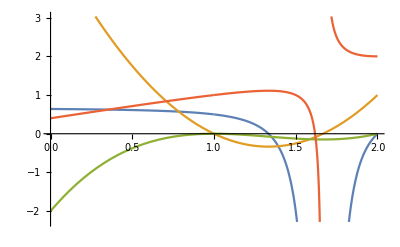

```mathematica
Plot[{φ'[x],f'[x],f[x],φ[x]},{x,0,2},PlotRange->Automatic]
```

```mathematica
Solve[f'[x]==0,x,Reals]
```

{{x→1},{x→5/3}}

```mathematica
Simplify[φ[x]]
```

(2+2 x-2 x^2)/(5-3 x)

```mathematica
g[x_]=(5-8 x+3 x^2)^2-(-8+6 x) (-2+5 x-4 x^2+x^3)
```

(5-8 x+3 x^2)^2-(-8+6 x) (-2+5 x-4 x^2+x^3)

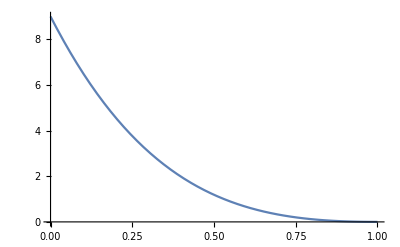

```mathematica
Plot[g[x],{x,0,1}]
```

```mathematica
Expand[(5-8 x+3 x^2)^2-(-8+6 x) (-2+5 x-4 x^2+x^3)]
```

9-28 x+32 x^2-16 x^3+3 x^4

```mathematica
g'[x]
```

(-8+6 x) (5-8 x+3 x^2)-6 (-2+5 x-4 x^2+x^3)

```mathematica
Expand[(-8+6 x) (5-8 x+3 x^2)-6 (-2+5 x-4 x^2+x^3)]
```

-28+64 x-48 x^2+12 x^3

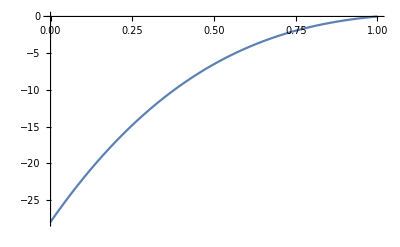

```mathematica
Plot[g'[x],{x,0,1}]
```

```mathematica
g''[x]
```

(-8+6 x)^2

```mathematica
g'[1]
```

0

```mathematica
g[1]
```

0